# Experiment 32a - Compton Scattering

```mathematica
<<CurveFit`
```

CurveFit for Mathematica v7.x thru v11.x, Version 1.96, 4/4/2018

Caltech Sophomore Physics Labs, Pasadena, CA

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 32a

## Energy calibration of MCA

### NaI detector

We construct an energy calibration function for the NaI scintillator using the full-energy peaks in the calibration data. We begin by removing noise from our calibration data.

```mathematica
calFiles=StringJoin["32a/",#]&/@{"ba133_cal_na.mca","co60_cal_na.mca","cs137_cal_na.mca","na22_cal_na.mca"};
errFiles=StringJoin["err_",#]&/@{"ba133_cal_na.mca","co60_cal_na.mca","cs137_cal_na.mca","na22_cal_na.mca"};
errFiles=StringJoin["32a/",#]&/@errFiles;
```

```mathematica
(* Add Poisson count errors to datafiles and export *)
For[i=1,i≤Length[calFiles],i++,(LoadFile[calFiles[[i]]];MakePoisson[Xerrors -> True];SaveFile[errFiles[[i]]])];
```

32a/ba133_cal_na.mca

File comment header:

Spectrum #00018	2:03:20 PM 6/7/2018  Time: 164.41 ; MCA 2

Ch  	Count

Read 1024 data points.

Sorted data in order of increasing X values.

1024 Y count values have had sigma values assigned.

1024 X channel values have had sigma values assigned.

Sorted data saved in 32a/err_ba133_cal_na.mca

32a/co60_cal_na.mca

File comment header:

Spectrum #00003	4:44:38 PM 6/7/2018  Time: 251.32 ; MCA 2

Ch  	Count

Read 1024 data points.

Sorted data in order of increasing X values.

1024 Y count values have had sigma values assigned.

1024 X channel values have had sigma values assigned.

Sorted data saved in 32a/err_co60_cal_na.mca

32a/cs137_cal_na.mca

File comment header:

Spectrum #00013	1:30:11 PM 6/7/2018  Time: 445.08 ; MCA 2

Ch  	Count

Read 1024 data points.

Sorted data in order of increasing X values.

1024 Y count values have had sigma values assigned.

1024 X channel values have had sigma values assigned.

Sorted data saved in 32a/err_cs137_cal_na.mca

32a/na22_cal_na.mca

File comment header:

Spectrum #00019	2:10:45 PM 6/7/2018  Time: 371.75 ; MCA 2

Ch  	Count

Read 1024 data points.

Sorted data in order of increasing X values.

1024 Y count values have had sigma values assigned.

1024 X channel values have had sigma values assigned.

Sorted data saved in 32a/err_na22_cal_na.mca

```mathematica
(* Add poisson count errors to noise and export *)
LoadFile["32a/noise_na.mca"];
MakePoisson[Xerrors->True];
SaveFile["32a/err_noise_na.mca"];
```

32a/noise_na.mca

File comment header:

Spectrum #00022	2:21:17 PM 6/7/2018  Time: 95.51 ; MCA 2

Ch  	Count

Read 1024 data points.

Sorted data in order of increasing X values.

1024 Y count values have had sigma values assigned.

1024 X channel values have had sigma values assigned.

Sorted data saved in 32a/err_noise_na.mca

```mathematica
(* Removing noise by normalizing over runtime, and subtracting noise and propagating errors. *)
runtimes=Table[StringSplit[Import[calFiles[[i]]][[1]]][[2]][[5]],{i,1,Length[calFiles]}]; 
runNoise=StringSplit[Import["32a/noise_na.mca"][[1]]][[2]][[5]];
```

```mathematica
norm=For[i=1,i≤Length[errFiles],i++,(file=Import[errFiles[[i]]];normFile=Table[{file[[j]][[1]],(file[[j]][[2]])/ToExpression[runtimes[[i]]],(file[[j]][[3]])/ToExpression[runtimes[[i]]],file[[j]][[4]]},{j,1,Length[file]}];Export[StringJoin["32a/norm_",StringJoin[FileBaseName[calFiles[[i]]]],".dat"],normFile];)];
```

```mathematica
file=Import["32a/err_noise_na.mca"];normFile=Table[{file[[j]][[1]],(file[[j]][[2]])/ToExpression[runNoise],(file[[j]][[3]])/ToExpression[runNoise],file[[j]][[4]]},{j,1,Length[file]}];Export[StringJoin["32a/norm_",StringJoin["noise_na"],".dat"],normFile];
```

```mathematica
(* Subtracting normalized noise from files *)
normList=StringJoin["32a/norm_",StringJoin[FileBaseName[#]],".dat"]&/@calFiles;
```

```mathematica
normNoise=Import["32a/norm_noise_na.dat"];
```

```mathematica
For[i=1,i≤Length[normList],i++,(file=Import[normList[[i]]];corrected=Table[{file[[j]][[1]],file[[j]][[2]]-normNoise[[j]][[2]],Sqrt[(file[[j]][[3]])^2+(normNoise[[j]][[3]])^2],Sqrt[(file[[j]][[4]])^2+(normNoise[[j]][[4]])^2]},{j,1,Length[file]}];Export[StringJoin["32a/corrected_",StringJoin[FileBaseName[calFiles[[i]]]],".dat"],corrected];)];
```

We now fit the full-energy peaks in the calibration data to construct our energy calibration function for the NaI detector.

#### Ba-133

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 32a/32a/corrected_ba133_cal_na.dat

Read 1024 data points.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{34.7,42.492}

n= 8

3 points removed.

```mathematica
GaussianCFit[]
```

n = 8

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
40.2731 | c= 
3.5809 | 
σ_y_max= 
33.3116 | σ_c= 
8.54695 | 
μ= 
38.4393 | sigma= 
2.01266 | 
σ_μ= 
0.168103 | σ_sigma= 
1.33571 | Std. deviation= 
4.18606

Fit of (x,y±σ_y)

y_max= 
39.862 | c= 
3.7507 | 
σ_y_max= 
0.996389 | σ_c= 
1.02015 | 
μ= 
38.5098 | sigma= 
1.98859 | 
σ_μ= 
0.0156777 | σ_sigma= 
0.0633369 | χ^2/(n-4)= 
96.6791

Fit of (x±σ_x,y±σ_y)

y_max= 
43.1832 | c= 
0.131782 | 
σ_y_max= 
4.89726 | σ_c= 
3.25158 | 
μ= 
38.3988 | sigma= 
2.20432 | 
σ_μ= 
0.0241879 | σ_sigma= 
0.202401 | χ^2/(n-4)= 
55.5576

```mathematica
calData={}; (* {energy in keV, channel, sigchannel, errenergy=0} *)
```

```mathematica
calData=AppendTo[calData,{32,mean,sigmean,0}];
```

```mathematica
Undo[]
```

corrected_ba133_cal_na.dat

n = 33

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{53.2895,76.63}

n= 23

10 points removed.

```mathematica
GaussianCFit[]
```

n = 23

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
100.086 | c= 
-44.576 | 
σ_y_max= 
124.239 | σ_c= 
124.459 | 
μ= 
66.1785 | sigma= 
14.9499 | 
σ_μ= 
0.0908924 | σ_sigma= 
8.31539 | Std. deviation= 
1.02451

Fit of (x,y±σ_y)

y_max= 
106.245 | c= 
-50.7844 | 
σ_y_max= 
39.9161 | σ_c= 
40.0531 | 
μ= 
66.2032 | sigma= 
15.483 | 
σ_μ= 
0.045437 | σ_sigma= 
3.03648 | χ^2/(n-4)= 
3.78963

Fit of (x±σ_x,y±σ_y)

y_max= 
105.844 | c= 
-50.377 | 
σ_y_max= 
41.9069 | σ_c= 
42.0441 | 
μ= 
66.1977 | sigma= 
15.4463 | 
σ_μ= 
0.0466827 | σ_sigma= 
3.17343 | χ^2/(n-4)= 
3.65628

```mathematica
calData=AppendTo[calData,{81,mean,sigmean,0}];
```

```mathematica
Undo[]
```

corrected_ba133_cal_na.dat

n = 363

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{231.46,288.324}

n= 56

5 points removed.

```mathematica
GaussianCFit[]
```

n = 56

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
23.1677 | c= 
2.23966 | 
σ_y_max= 
0.229126 | σ_c= 
0.240249 | 
μ= 
249.757 | sigma= 
16.3773 | 
σ_μ= 
0.0760808 | σ_sigma= 
0.200316 | Std. deviation= 
0.316796

Fit of (x,y±σ_y)

y_max= 
23.2766 | c= 
2.08541 | 
σ_y_max= 
0.155064 | σ_c= 
0.166417 | 
μ= 
249.735 | sigma= 
16.5231 | 
σ_μ= 
0.081704 | σ_sigma= 
0.173595 | χ^2/(n-4)= 
1.30888

Fit of (x±σ_x,y±σ_y)

y_max= 
23.2849 | c= 
2.07769 | 
σ_y_max= 
0.157672 | σ_c= 
0.168828 | 
μ= 
249.737 | sigma= 
16.5276 | 
σ_μ= 
0.0828655 | σ_sigma= 
0.176052 | χ^2/(n-4)= 
1.26494

```mathematica
calData=AppendTo[calData,{356,mean,sigmean,0}];
```

#### Cs-137

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 32a/32a/corrected_cs137_cal_na.dat

Read 1024 data points.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{32.275,42.815}

n= 10

8 points removed.

```mathematica
GaussianCFit[]
```

n = 10

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
4.09278 | c= 
0.587897 | 
σ_y_max= 
0.390885 | σ_c= 
0.28955 | 
μ= 
38.3889 | sigma= 
1.67189 | 
σ_μ= 
0.143293 | σ_sigma= 
0.225226 | Std. deviation= 
0.423841

Fit of (x,y±σ_y)

y_max= 
4.06819 | c= 
0.717621 | 
σ_y_max= 
0.120248 | σ_c= 
0.048511 | 
μ= 
38.4348 | sigma= 
1.52804 | 
σ_μ= 
0.0420012 | σ_sigma= 
0.0473946 | χ^2/(n-4)= 
9.25172

Fit of (x±σ_x,y±σ_y)

y_max= 
4.05029 | c= 
0.716822 | 
σ_y_max= 
0.121583 | σ_c= 
0.0518228 | 
μ= 
38.4125 | sigma= 
1.54667 | 
σ_μ= 
0.046413 | σ_sigma= 
0.055099 | χ^2/(n-4)= 
8.46881

```mathematica
calData=AppendTo[calData,{32,mean,sigmean,0}];
```

```mathematica
Undo[]
```

corrected_cs137_cal_na.dat

n = 1024

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{409.,507.4}

n= 99

925 points removed.

```mathematica
GaussianCFit[]
```

n = 99

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
3.04408 | c= 
0.0693182 | 
σ_y_max= 
0.0193572 | σ_c= 
0.0185122 | 
μ= 
460.386 | sigma= 
17.9983 | 
σ_μ= 
0.0885457 | σ_sigma= 
0.168813 | Std. deviation= 
0.0596712

Fit of (x,y±σ_y)

y_max= 
3.05587 | c= 
0.0516781 | 
σ_y_max= 
0.017829 | σ_c= 
0.0121158 | 
μ= 
460.203 | sigma= 
18.141 | 
σ_μ= 
0.0899075 | σ_sigma= 
0.147984 | χ^2/(n-4)= 
1.07384

Fit of (x±σ_x,y±σ_y)

y_max= 
3.05565 | c= 
0.0519694 | 
σ_y_max= 
0.0180369 | σ_c= 
0.0122043 | 
μ= 
460.199 | sigma= 
18.1368 | 
σ_μ= 
0.0919252 | σ_sigma= 
0.149873 | χ^2/(n-4)= 
1.05013

```mathematica
calData=AppendTo[calData,{661,mean,sigmean,0}];
```

#### Na-22

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 32a/32a/corrected_na22_cal_na.dat

Read 1024 data points.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{334.4,385.4}

n= 51

973 points removed.

```mathematica
GaussianCFit[]
```

n = 51

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

Calculating sigy

y_max= 
0.67416 | c= 
-0.266285 | 
σ_y_max= 
0.866679 | σ_c= 
0.835706 | 
μ= 
357.203 | sigma= 
23.09 | 
σ_μ= 
0.462295 | σ_sigma= 
14.2739 | Std. deviation= 
0.0401459

Fit of (x,y±σ_y)

y_max= 
0.708359 | c= 
-0.298423 | 
σ_y_max= 
0.664992 | σ_c= 
0.877934 | 
μ= 
357.611 | sigma= 
23.431 | 
σ_μ= 
0.398379 | σ_sigma= 
14.5399 | χ^2/(n-4)= 
1.12109

Fit of (x±σ_x,y±σ_y)

y_max= 
0.720265 | c= 
-0.310486 | 
σ_y_max= 
0.664474 | σ_c= 
0.949795 | 
μ= 
357.59 | sigma= 
23.7044 | 
σ_μ= 
0.399515 | σ_sigma= 
15.4023 | χ^2/(n-4)= 
1.10838

```mathematica
calData=AppendTo[calData,{511,mean,sigmean,0}];
```

The Na-22 data seems very prone to noise, therefore we only use the 0.522 MeV annihilation peak for calibration (the others features are buried in noise. Although the non noise-corrected spectrum is cleaner, this is an indication that the calibration data collected for Na-22 is of poor quality so we neglect the other features in the calibration. ).

#### Co-60

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 32a/32a/corrected_co60_cal_na.dat

Read 1024 data points.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{792.2,884.8}

n= 92

932 points removed.

```mathematica
GaussianCFit[]
```

n = 92

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
0.394041 | c= 
0.0967931 | 
σ_y_max= 
0.0264512 | σ_c= 
0.0236135 | 
μ= 
834.101 | sigma= 
22.0949 | 
σ_μ= 
0.515534 | σ_sigma= 
1.75149 | Std. deviation= 
0.0397197

Fit of (x,y±σ_y)

y_max= 
0.392083 | c= 
0.0964254 | 
σ_y_max= 
0.0182627 | σ_c= 
0.0172713 | 
μ= 
833.968 | sigma= 
21.8038 | 
σ_μ= 
0.482805 | σ_sigma= 
1.39908 | χ^2/(n-4)= 
1.17829

Fit of (x±σ_x,y±σ_y)

y_max= 
0.392422 | c= 
0.0961705 | 
σ_y_max= 
0.0183437 | σ_c= 
0.0173298 | 
μ= 
833.969 | sigma= 
21.8167 | 
σ_μ= 
0.483748 | σ_sigma= 
1.40377 | χ^2/(n-4)= 
1.17257

```mathematica
calData=AppendTo[calData,{1173,mean,sigmean,0}];
```

```mathematica
Undo[]
```

corrected_co60_cal_na.dat

n = 1024

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{900.2,993.6}

n= 93

931 points removed.

```mathematica
GaussianCFit[]
```

n = 93

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
0.380359 | c= 
0.00539245 | 
σ_y_max= 
0.0370951 | σ_c= 
0.0301675 | 
μ= 
944.082 | sigma= 
25.1937 | 
σ_μ= 
0.488099 | σ_sigma= 
2.43508 | Std. deviation= 
0.033173

Fit of (x,y±σ_y)

y_max= 
0.379097 | c= 
0.00205103 | 
σ_y_max= 
0.0313713 | σ_c= 
0.026475 | 
μ= 
943.815 | sigma= 
25.5032 | 
σ_μ= 
0.469695 | σ_sigma= 
2.27966 | χ^2/(n-4)= 
0.937202

Fit of (x±σ_x,y±σ_y)

y_max= 
0.379394 | c= 
0.00178479 | 
σ_y_max= 
0.0315378 | σ_c= 
0.0265682 | 
μ= 
943.816 | sigma= 
25.517 | 
σ_μ= 
0.470608 | σ_sigma= 
2.28797 | χ^2/(n-4)= 
0.934094

```mathematica
calData=AppendTo[calData,{1332,mean,sigmean,0}];
```

#### Constructing the calibration function

```mathematica
(* Combine 32 keV datapoints. *)
calData[[1]]={32,Mean[{calData[[1]][[2]],calData[[4]][[2]]}],Sqrt[(calData[[1]][[3]])^2+(calData[[4]][[3]])^2]/2,0};
```

```mathematica
calData=Delete[calData,4];
```

```mathematica
Export["32a/cal_data.dat",calData];
```

```mathematica
calTable=Join[{{"Energy (keV)","Channel Number"}},Table[{StringReplace["%1",{"%1"->ToString[NumberForm[calData[[i]][[1]],3]]}],StringReplace["%1 ± %2",{"%1"->ToString[NumberForm[calData[[i]][[2]],3]],"%2"->ToString[NumberForm[calData[[i]][[3]],2]]}]},{i,1,Length[calData]}]];
Grid[calTable,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]
```

Energy (keV) | Channel Number
32 | 38.4 ± 0.026
81 | 66.2 ± 0.047
356 | 250. ± 0.083
661 | 460. ± 0.092
511 | 358. ± 0.4
1173 | 834. ± 0.48
1332 | 944. ± 0.47

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 32a/32a/cal_data.dat

LoadFile::sorted: Data sorted in increasing x order.

Read 7 data points.

```mathematica
SwitchXXandYY[]
```

xx and yy have been switched (so have sx and sy).

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{19.5065,418.4}

n= 4

3 points removed.

```mathematica
QuadraticFit[]
```

n = 4

y(x) = a + b x + c x^2

Fit of (x,y)  (unweighted)

a= 
-27.5939 | b= 
1.62053 | c= 
-0.000322961 | 
σ_a= 
4.94201 | σ_b= 
0.0775489 | σ_c= 
0.000197956 | Std. deviation= 
3.64384

Fit of (x±σ_x,y±σ_y)

a= 
-33.3313 | b= 
1.74233 | c= 
-0.000707733 | 
σ_a= 
0.119738 | σ_b= 
0.00289677 | σ_c= 
9.43175×10^-6 | χ^2/(n-3)= 
1666.42

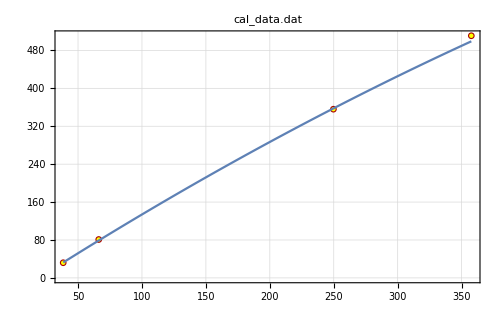
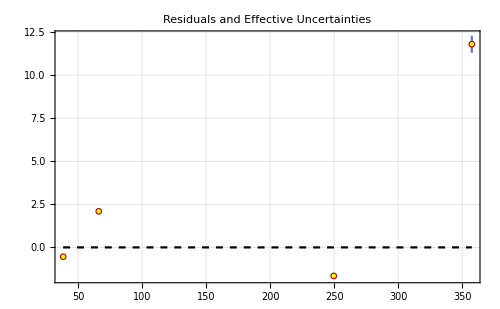
-Graphics-
-Graphics-
y(x) = a + b x + c x^2
a= 
-33.3313 | b= 
1.74233 | c= 
-0.000707733 | 
σ_a= 
0.119738 | σ_b= 
0.00289677 | σ_c= 
9.43175×10^-6 | χ^2/(n-3)= 
1666.42

```mathematica
LinearDifferencePlot[]
```

```mathematica
Undo[]
```

cal_data.dat

n = 7

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{345.2,963.159}

n= 4

3 points removed.

```mathematica
LinearFit[]
```

n = 4

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
16.2403 | b= 
1.39162 | 
σ_a= 
6.84102 | σ_b= 
0.0098589 | Std. deviation= 
4.84571

Fit of (x±σ_x,y±σ_y)

a= 
22.943 | b= 
1.38535 | 
σ_a= 
0.535681 | σ_b= 
0.001081 | χ^2/(n-2)= 
129.9

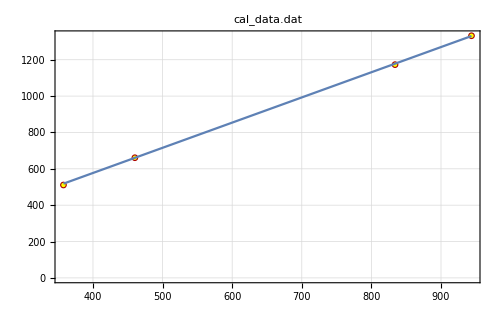
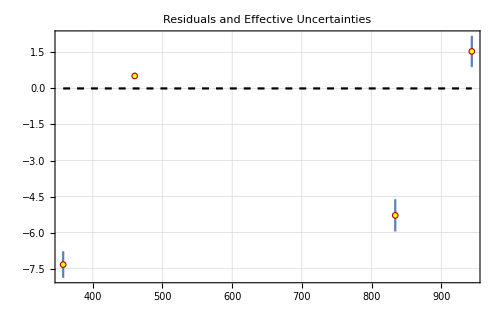
-Graphics-
-Graphics-
y(x) = a + b x
a= 
22.943 | b= 
1.38535 | 
σ_a= 
0.535681 | σ_b= 
0.001081 | χ^2/(n-2)= 
129.9

```mathematica
LinearDifferencePlot[]
```

```mathematica
calibration[channel_]:={Piecewise[{{-33.331281248295426+1.7423347894608627 channel[[1]]+-0.0007077325790811842 channel[[1]]^2,channel[[1]]<300},{22.943046857142885+1.3853510522657388 channel[[1]],channel[[1]]≥300}}],Piecewise[{{Sqrt[0.11973843181390834^2+channel[[1]]^2 0.002896772825801799^2+1.7423347894608627 channel[[2]]^2+(-0.0007077325790811842 channel[[1]]^2)^2(((9.431753627773405*^-6)/-0.0007077325790811842)^2+(2 channel[[2]]/channel[[1]])^2)],channel[[1]]<300},{Sqrt[0.5356805976904518^2+channel[[1]]^2 0.0010809983159092101^2+channel[[2]]^2 1.3853510522657388^2],channel[[1]]≥300}}]};
```

## Energy as a function of scattering angle

The following work is done in the “Exp32.nb” notebook provided for analyzing scattering events.

### 40 degrees

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 32a/32a/scatter_40.xy.mca

File comment header:

Spectrum #00004	3:03:43 PM 6/7/2018  Time: 626.36 ; XY Scatter Event Data
40 deg
X Ch	Y Ch

LoadFile::sorted: Data sorted in increasing x order.

Read 4298 data points.

n = 1362

Undo[] to return to previous data set.

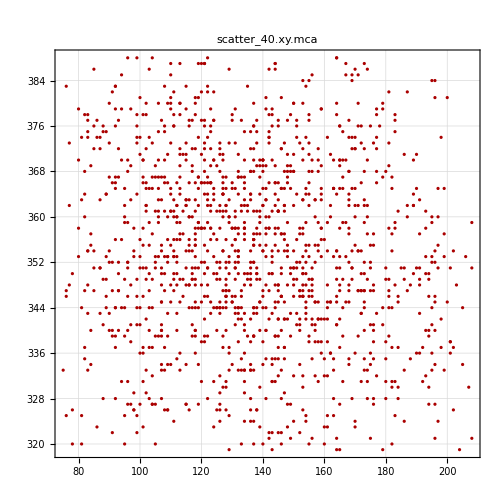

```mathematica
KeepXY[]
```

n = 133

Sorted data in order of increasing X values.

133 Y count values have had sigma values assigned.

Undo[] once to get rid of channel count sigmas.

Undo[] again to return to Scatter Data.

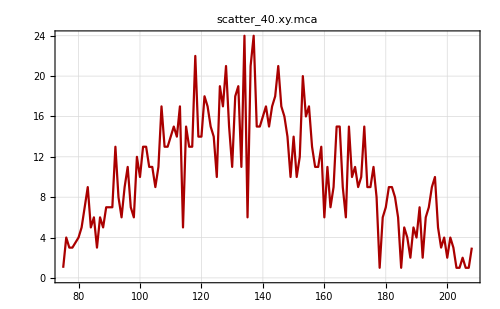

```mathematica
xy2x[]
```

```mathematica
GaussianCFit[]
```

n = 133

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
15.7997 | c= 
0.802434 | 
σ_y_max= 
2.19985 | σ_c= 
1.6158 | 
μ= 
134.288 | sigma= 
33.4861 | 
σ_μ= 
1.29103 | σ_sigma= 
5.09418 | Std. deviation= 
3.11307

Fit of (x,y±σ_y)

y_max= 
14.9556 | c= 
0.695793 | 
σ_y_max= 
0.774352 | σ_c= 
0.632289 | 
μ= 
132.636 | sigma= 
30.3599 | 
σ_μ= 
1.11627 | σ_sigma= 
2.31373 | χ^2/(n-4)= 
1.34211

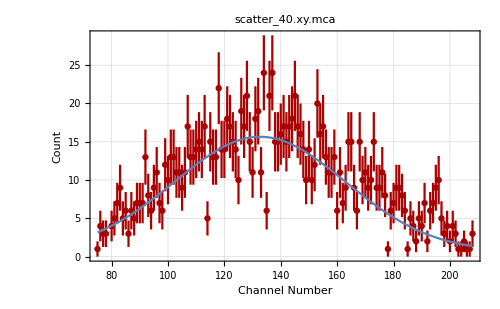
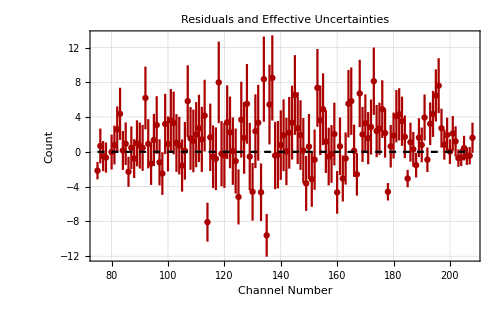
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
14.9556 | c= 
0.695793 | 
σ_y_max= 
0.774352 | σ_c= 
0.632289 | 
μ= 
132.636 | sigma= 
30.3599 | 
σ_μ= 
1.11627 | σ_sigma= 
2.31373 | χ^2/(n-4)= 
1.34211

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

```mathematica
xData={};
```

```mathematica
AppendTo[xData,{40,mean,sigmean}];
```

```mathematica
Undo[]
```

scatter_40.xy.mca

n = 1362

n = 70

Sorted data in order of increasing X values.

70 Y count values have had sigma values assigned.

Undo[] once to get rid of channel count sigmas.

Undo[] again to return to Scatter Data.

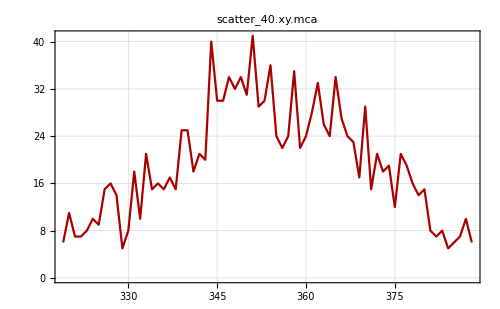

```mathematica
xy2y[]
```

```mathematica
GaussianCFit[]
```

n = 70

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
28.2107 | c= 
2.94049 | 
σ_y_max= 
4.07119 | σ_c= 
3.58358 | 
μ= 
354.123 | sigma= 
17.0228 | 
σ_μ= 
0.741904 | σ_sigma= 
2.71974 | Std. deviation= 
4.64457

Fit of (x,y±σ_y)

y_max= 
26.4203 | c= 
4.10615 | 
σ_y_max= 
2.08407 | σ_c= 
1.73134 | 
μ= 
354.386 | sigma= 
15.4963 | 
σ_μ= 
0.647671 | σ_sigma= 
1.81144 | χ^2/(n-4)= 
1.10695

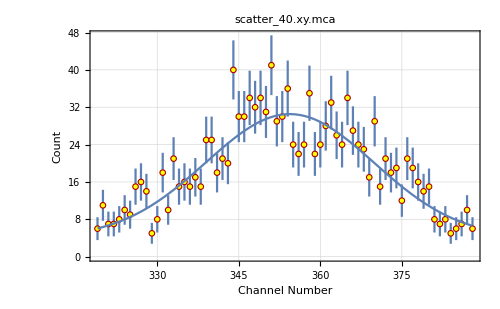
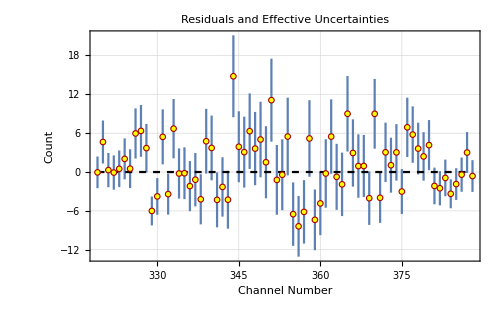
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
26.4203 | c= 
4.10615 | 
σ_y_max= 
2.08407 | σ_c= 
1.73134 | 
μ= 
354.386 | sigma= 
15.4963 | 
σ_μ= 
0.647671 | σ_sigma= 
1.81144 | χ^2/(n-4)= 
1.10695

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

```mathematica
yData={};
```

```mathematica
AppendTo[yData,{40,mean,sigmean}];
```

### 60 degrees

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 32a/32a/scatter_60.xy.mca

File comment header:

Spectrum #00006	3:30:22 PM 6/7/2018  Time: 553.36 ; XY Scatter Event Data
60 deg
X Ch	Y Ch

LoadFile::sorted: Data sorted in increasing x order.

Read 2996 data points.

n = 1003

Undo[] to return to previous data set.

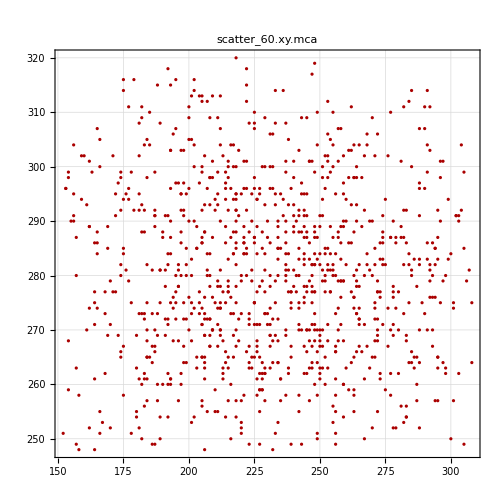

```mathematica
KeepXY[]
```

n = 157

Sorted data in order of increasing X values.

157 Y count values have had sigma values assigned.

Undo[] once to get rid of channel count sigmas.

Undo[] again to return to Scatter Data.

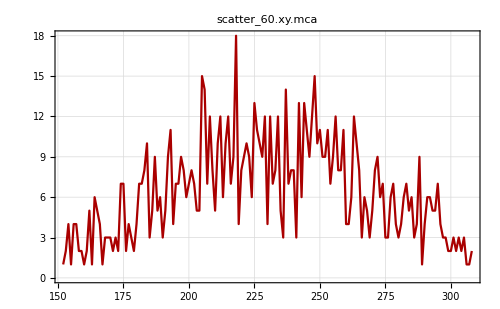

```mathematica
xy2x[]
```

```mathematica
NRangeRemove[#]&/@{ 67,68,79,90}
```

n= 156

1 point removed.

n= 155

1 point removed.

n= 154

1 point removed.

n= 153

1 point removed.

{Null,Null,Null,Null}

```mathematica
GaussianCFit[]
```

n = 153

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
10.803 | c= 
-1.33814 | 
σ_y_max= 
8.28419 | σ_c= 
8.51633 | 
μ= 
231.143 | sigma= 
50.559 | 
σ_μ= 
1.93265 | σ_sigma= 
25.671 | Std. deviation= 
2.47254

Fit of (x,y±σ_y)

y_max= 
9.29206 | c= 
-1.14376 | 
σ_y_max= 
3.66407 | σ_c= 
3.90427 | 
μ= 
231.659 | sigma= 
48.527 | 
σ_μ= 
1.69465 | σ_sigma= 
15.8216 | χ^2/(n-4)= 
1.05839

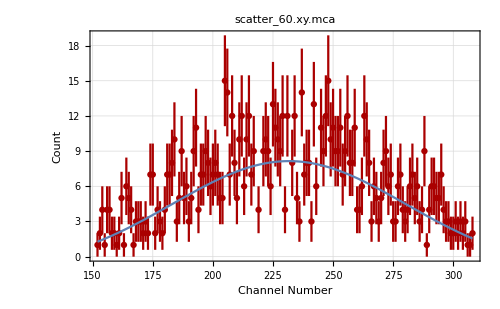
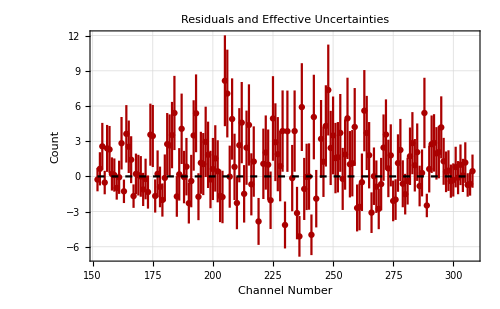
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
9.29206 | c= 
-1.14376 | 
σ_y_max= 
3.66407 | σ_c= 
3.90427 | 
μ= 
231.659 | sigma= 
48.527 | 
σ_μ= 
1.69465 | σ_sigma= 
15.8216 | χ^2/(n-4)= 
1.05839

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

```mathematica
AppendTo[xData,{60,mean,sigmean}];
```

```mathematica
Undo[]
```

scatter_60.xy.mca

n = 1003

n = 73

Sorted data in order of increasing X values.

73 Y count values have had sigma values assigned.

Undo[] once to get rid of channel count sigmas.

Undo[] again to return to Scatter Data.

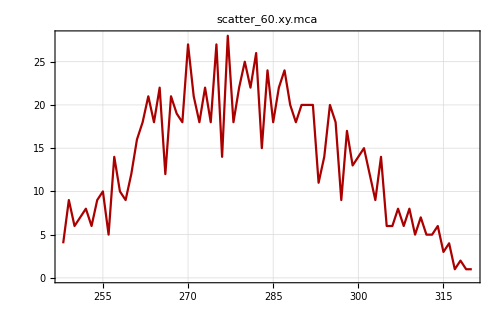

```mathematica
xy2y[]
```

```mathematica
GaussianCFit[]
```

n = 73

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
24.9823 | c= 
-2.58455 | 
σ_y_max= 
4.57494 | σ_c= 
4.87688 | 
μ= 
279.377 | sigma= 
20.8536 | 
σ_μ= 
0.68154 | σ_sigma= 
3.50933 | Std. deviation= 
3.15897

Fit of (x,y±σ_y)

y_max= 
24.2247 | c= 
-2.69883 | 
σ_y_max= 
2.41656 | σ_c= 
2.82003 | 
μ= 
279.698 | sigma= 
20.6341 | 
σ_μ= 
0.692554 | σ_sigma= 
2.62177 | χ^2/(n-4)= 
0.745444

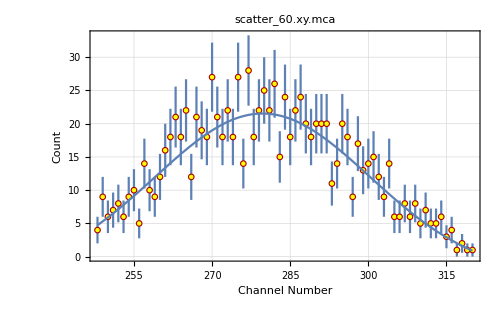
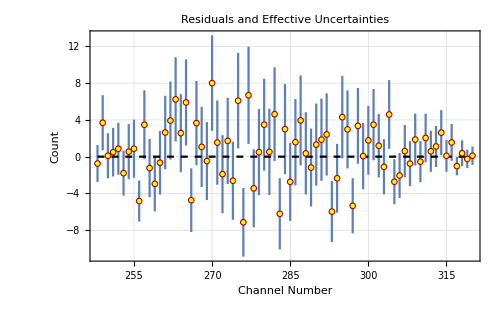
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
24.2247 | c= 
-2.69883 | 
σ_y_max= 
2.41656 | σ_c= 
2.82003 | 
μ= 
279.698 | sigma= 
20.6341 | 
σ_μ= 
0.692554 | σ_sigma= 
2.62177 | χ^2/(n-4)= 
0.745444

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

```mathematica
AppendTo[yData,{60,mean,sigmean}];
```

### 80 degrees

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 32a/32a/scatter_80.xy.mca

File comment header:

Spectrum #00008	4:06:47 PM 6/7/2018  Time: 1454.27 ; XY Scatter Event Data
80 deg
X Ch	Y Ch

LoadFile::sorted: Data sorted in increasing x order.

Read 6086 data points.

n = 2129

Undo[] to return to previous data set.

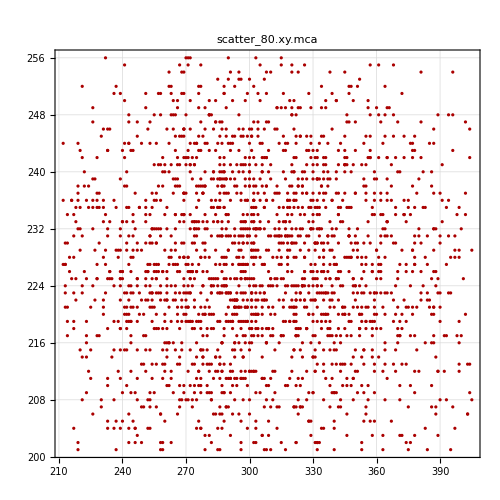

```mathematica
KeepXY[]
```

n = 194

Sorted data in order of increasing X values.

194 Y count values have had sigma values assigned.

Undo[] once to get rid of channel count sigmas.

Undo[] again to return to Scatter Data.

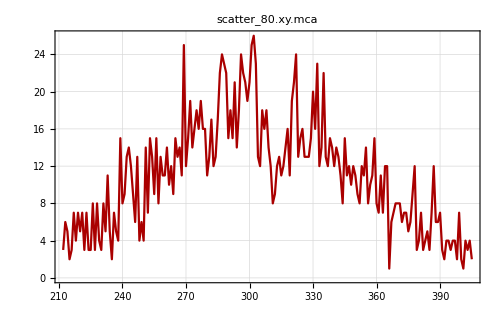

```mathematica
xy2x[]
```

```mathematica
GaussianCFit[]
```

n = 194

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
16.1134 | c= 
1.60426 | 
σ_y_max= 
1.85277 | σ_c= 
1.43838 | 
μ= 
302.021 | sigma= 
46.9047 | 
σ_μ= 
1.60672 | σ_sigma= 
6.10737 | Std. deviation= 
3.4042

Fit of (x,y±σ_y)

y_max= 
15.207 | c= 
1.69228 | 
σ_y_max= 
0.761096 | σ_c= 
0.663175 | 
μ= 
302.345 | sigma= 
42.1452 | 
σ_μ= 
1.36054 | σ_sigma= 
3.19759 | χ^2/(n-4)= 
1.21439

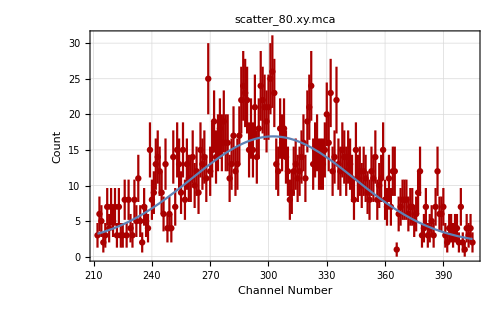
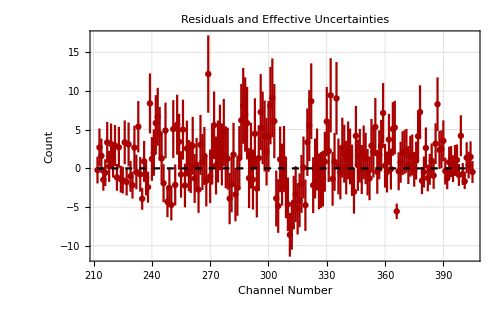
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
15.207 | c= 
1.69228 | 
σ_y_max= 
0.761096 | σ_c= 
0.663175 | 
μ= 
302.345 | sigma= 
42.1452 | 
σ_μ= 
1.36054 | σ_sigma= 
3.19759 | χ^2/(n-4)= 
1.21439

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

```mathematica
AppendTo[xData,{80,mean,sigmean}];
```

```mathematica
Undo[]
```

scatter_80.xy.mca

n = 2129

n = 56

Sorted data in order of increasing X values.

56 Y count values have had sigma values assigned.

Undo[] once to get rid of channel count sigmas.

Undo[] again to return to Scatter Data.

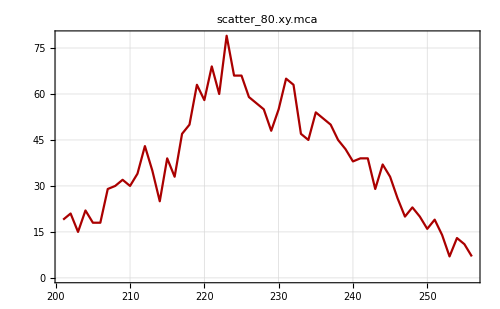

```mathematica
xy2y[]
```

```mathematica
GaussianCFit[]
```

n = 56

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
56.2881 | c= 
5.68518 | 
σ_y_max= 
6.10719 | σ_c= 
4.8607 | 
μ= 
226.634 | sigma= 
13.3327 | 
σ_μ= 
0.44207 | σ_sigma= 
1.69203 | Std. deviation= 
6.28071

Fit of (x,y±σ_y)

y_max= 
58.7817 | c= 
1.17445 | 
σ_y_max= 
4.93753 | σ_c= 
4.13823 | 
μ= 
226.749 | sigma= 
14.4076 | 
σ_μ= 
0.387345 | σ_sigma= 
1.56972 | χ^2/(n-4)= 
1.04349

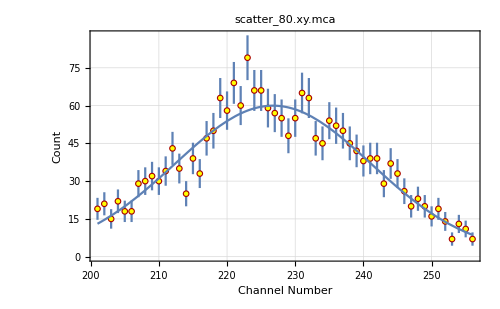
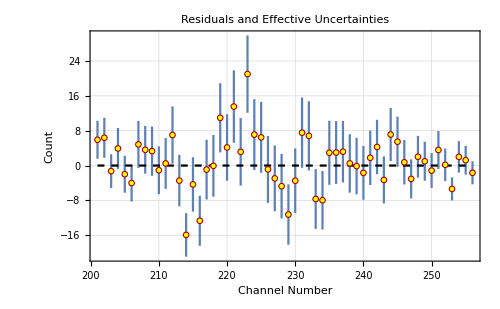
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
58.7817 | c= 
1.17445 | 
σ_y_max= 
4.93753 | σ_c= 
4.13823 | 
μ= 
226.749 | sigma= 
14.4076 | 
σ_μ= 
0.387345 | σ_sigma= 
1.56972 | χ^2/(n-4)= 
1.04349

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

```mathematica
AppendTo[yData,{80,mean,sigmean}];
```

### 100 degrees

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 32a/32a/scatter_100.xy.mca

File comment header:

Spectrum #00009	4:16:26 PM 6/7/2018  Time: 528.96 ; XY Scatter Event Data
100 deg
X Ch	Y Ch

LoadFile::sorted: Data sorted in increasing x order.

Read 2012 data points.

n = 704

Undo[] to return to previous data set.

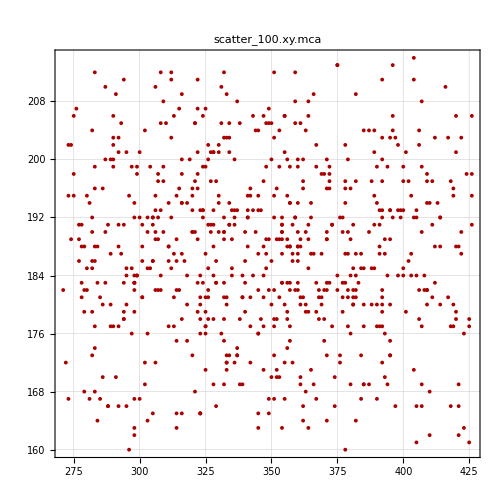

```mathematica
KeepXY[]
```

n = 154

Sorted data in order of increasing X values.

154 Y count values have had sigma values assigned.

Undo[] once to get rid of channel count sigmas.

Undo[] again to return to Scatter Data.

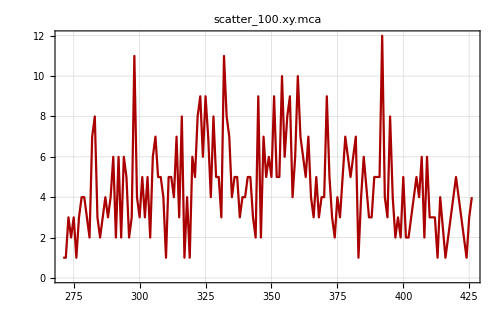

```mathematica
xy2x[]
```

```mathematica
NRangeRemove[#]&/@{28}
```

n= 152

1 point removed.

{Null}

```mathematica
GaussianCFit[]
```

n = 152

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
3.81682 | c= 
2.00889 | 
σ_y_max= 
4.49785 | σ_c= 
1.07168 | 
μ= 
345.316 | sigma= 
43.1507 | 
σ_μ= 
3.81612 | σ_sigma= 
71.4142 | Std. deviation= 
1.93879

Fit of (x,y±σ_y)

y_max= 
3.08151 | c= 
1.60418 | 
σ_y_max= 
2.43344 | σ_c= 
0.876048 | 
μ= 
349.291 | sigma= 
40.6876 | 
σ_μ= 
4.44023 | σ_sigma= 
3649.19 | χ^2/(n-4)= 
0.988598

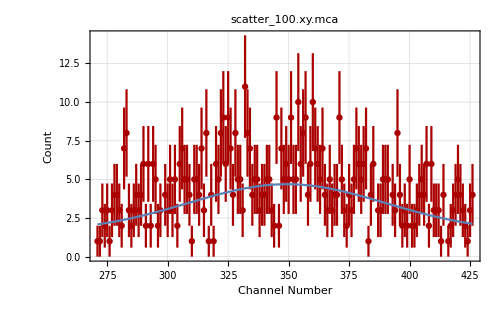
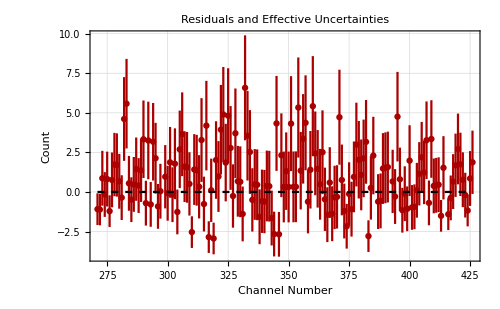
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
3.08151 | c= 
1.60418 | 
σ_y_max= 
2.43344 | σ_c= 
0.876048 | 
μ= 
349.291 | sigma= 
40.6876 | 
σ_μ= 
4.44023 | σ_sigma= 
3649.19 | χ^2/(n-4)= 
0.988598

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

```mathematica
AppendTo[xData,{100,mean,sigmean}];
```

```mathematica
Undo[]
```

scatter_100.xy.mca

n = 704

n = 55

Sorted data in order of increasing X values.

55 Y count values have had sigma values assigned.

Undo[] once to get rid of channel count sigmas.

Undo[] again to return to Scatter Data.

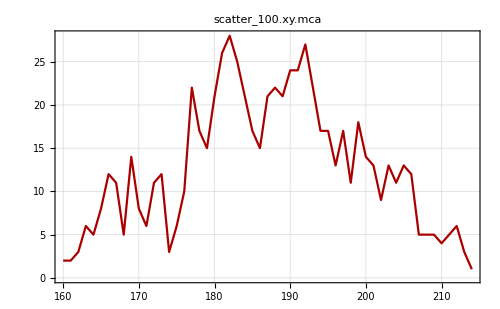

```mathematica
xy2y[]
```

```mathematica
GaussianCFit[]
```

n = 55

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
19.8858 | c= 
2.61267 | 
σ_y_max= 
2.79576 | σ_c= 
2.04741 | 
μ= 
187.536 | sigma= 
11.4252 | 
σ_μ= 
0.690038 | σ_sigma= 
2.27368 | Std. deviation= 
3.79403

Fit of (x,y±σ_y)

y_max= 
19.7508 | c= 
1.8952 | 
σ_y_max= 
1.28756 | σ_c= 
0.92032 | 
μ= 
188.513 | sigma= 
10.7196 | 
σ_μ= 
0.574773 | σ_sigma= 
1.24045 | χ^2/(n-4)= 
1.46893

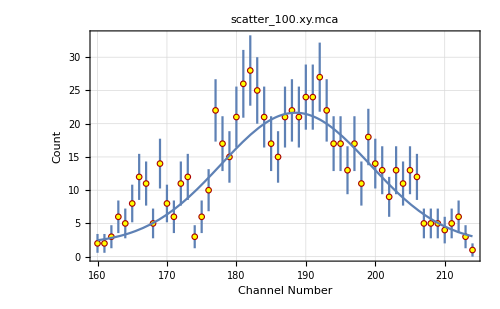
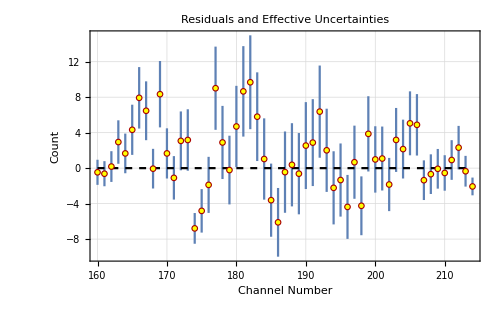
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
19.7508 | c= 
1.8952 | 
σ_y_max= 
1.28756 | σ_c= 
0.92032 | 
μ= 
188.513 | sigma= 
10.7196 | 
σ_μ= 
0.574773 | σ_sigma= 
1.24045 | χ^2/(n-4)= 
1.46893

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

```mathematica
AppendTo[yData,{100,mean,sigmean}];
```

### 120 degrees

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 32a/32a/scatter_120.xy.mca

File comment header:

Spectrum #00007	3:40:55 PM 6/7/2018  Time: 567.75 ; XY Scatter Event Data
120 deg
X Ch	Y Ch

LoadFile::sorted: Data sorted in increasing x order.

Read 2175 data points.

n = 1038

Undo[] to return to previous data set.

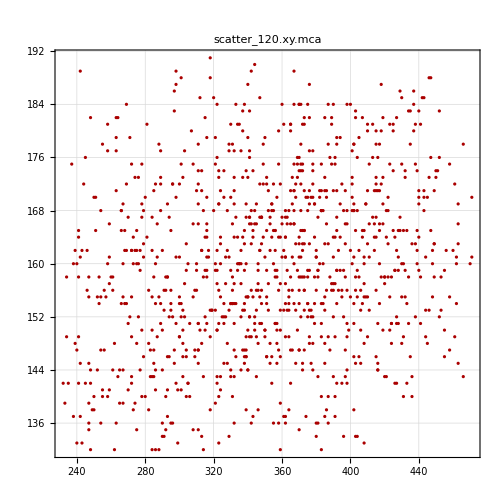

```mathematica
KeepXY[]
```

n = 230

Sorted data in order of increasing X values.

230 Y count values have had sigma values assigned.

Undo[] once to get rid of channel count sigmas.

Undo[] again to return to Scatter Data.

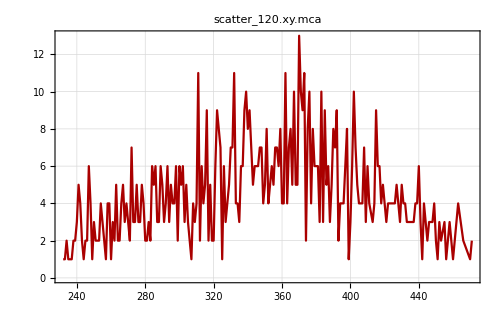

```mathematica
xy2x[]
```

```mathematica
GaussianCFit[]
```

n = 230

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
4.65221 | c= 
2.00546 | 
σ_y_max= 
0.827404 | σ_c= 
0.558659 | 
μ= 
359.561 | sigma= 
51.1911 | 
σ_μ= 
3.38108 | σ_sigma= 
11.8937 | Std. deviation= 
1.92458

Fit of (x,y±σ_y)

Calculating sigm

y_max= 
3.99783 | c= 
1.30416 | 
σ_y_max= 
1.27369 | σ_c= 
0.584287 | 
μ= 
360.741 | sigma= 
56.8461 | 
σ_μ= 
4.24652 | σ_sigma= 
22.1567 | χ^2/(n-4)= 
0.880585

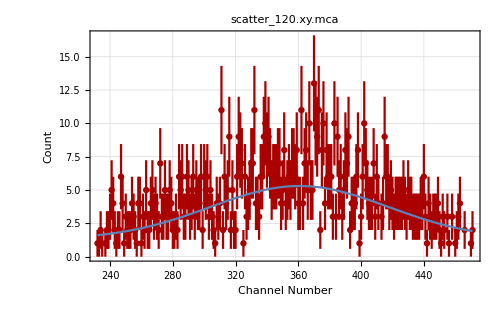
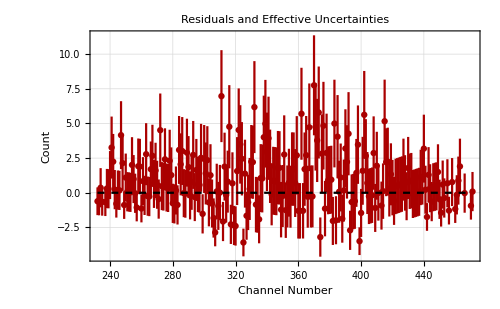
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
3.99783 | c= 
1.30416 | 
σ_y_max= 
1.27369 | σ_c= 
0.584287 | 
μ= 
360.741 | sigma= 
56.8461 | 
σ_μ= 
4.24652 | σ_sigma= 
22.1567 | χ^2/(n-4)= 
0.880585

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

```mathematica
AppendTo[xData,{120,mean,sigmean}];
```

```mathematica
Undo[]
```

scatter_120.xy.mca

n = 1038

n = 60

Sorted data in order of increasing X values.

60 Y count values have had sigma values assigned.

Undo[] once to get rid of channel count sigmas.

Undo[] again to return to Scatter Data.

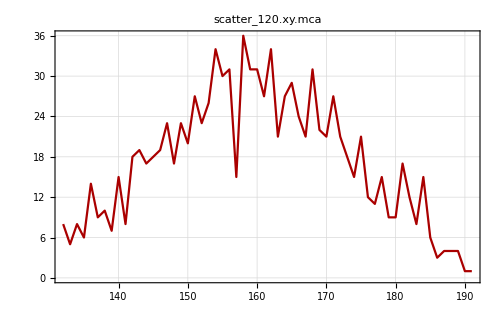

```mathematica
xy2y[]
```

```mathematica
GaussianCFit[]
```

n = 60

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
29.8781 | c= 
-0.972133 | 
σ_y_max= 
5.42878 | σ_c= 
5.90122 | 
μ= 
159.402 | sigma= 
15.4888 | 
σ_μ= 
0.571933 | σ_sigma= 
2.86305 | Std. deviation= 
3.94907

Fit of (x,y±σ_y)

y_max= 
32.1203 | c= 
-4.69935 | 
σ_y_max= 
3.6568 | σ_c= 
4.22351 | 
μ= 
159.316 | sigma= 
17.1331 | 
σ_μ= 
0.496917 | σ_sigma= 
2.34467 | χ^2/(n-4)= 
0.96631

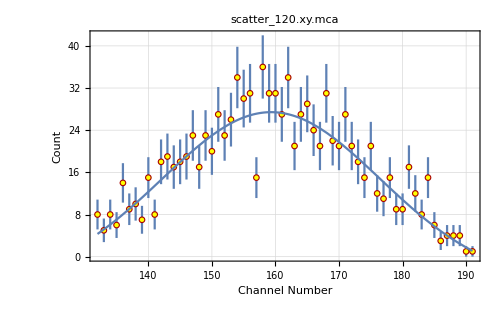
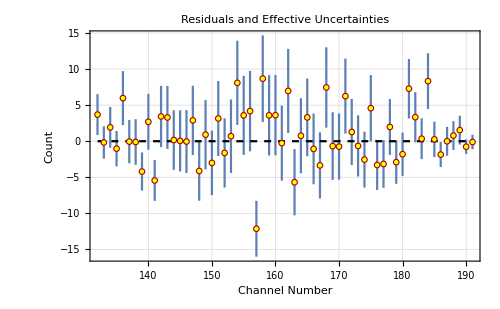
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
32.1203 | c= 
-4.69935 | 
σ_y_max= 
3.6568 | σ_c= 
4.22351 | 
μ= 
159.316 | sigma= 
17.1331 | 
σ_μ= 
0.496917 | σ_sigma= 
2.34467 | χ^2/(n-4)= 
0.96631

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

```mathematica
AppendTo[yData,{120,mean,sigmean}];
```

### 130 degrees

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 32a/32a/scatter_130.xy.mca

File comment header:

Spectrum #00011	4:36:41 PM 6/7/2018  Time: 486.44 ; XY Scatter Event Data
130 deg
X Ch	Y Ch

LoadFile::sorted: Data sorted in increasing x order.

Read 1943 data points.

n = 702

Undo[] to return to previous data set.

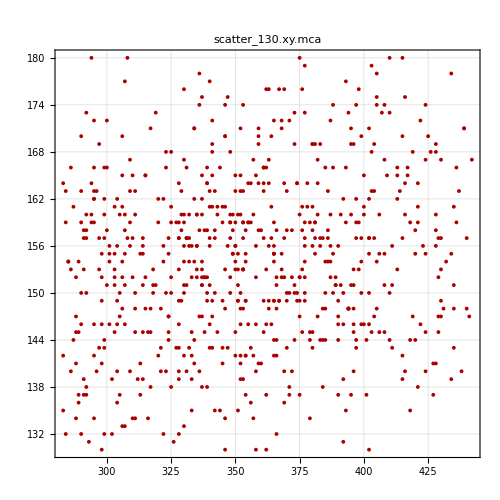

```mathematica
KeepXY[]
```

n = 158

Sorted data in order of increasing X values.

158 Y count values have had sigma values assigned.

Undo[] once to get rid of channel count sigmas.

Undo[] again to return to Scatter Data.

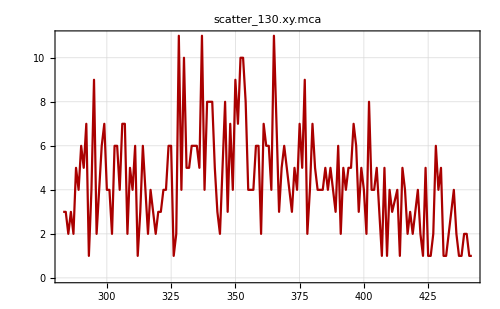

```mathematica
xy2x[]
```

```mathematica
NRangeRemove[#]&/@{13,46}
```

n= 157

1 point removed.

n= 156

1 point removed.

{Null,Null}

```mathematica
GaussianCFit[]
```

n = 156

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
4.97327 | c= 
0.85772 | 
σ_y_max= 
10.5364 | σ_c= 
1.56921 | 
μ= 
349.626 | sigma= 
53.0201 | 
σ_μ= 
3.65075 | σ_sigma= 
79.205 | Std. deviation= 
1.98057

Fit of (x,y±σ_y)

y_max= 
4.26556 | c= 
0.496153 | 
σ_y_max= 
4.28188 | σ_c= 
1.06997 | 
μ= 
352.543 | sigma= 
49.8594 | 
σ_μ= 
3.65033 | σ_sigma= 
40.9078 | χ^2/(n-4)= 
0.982867

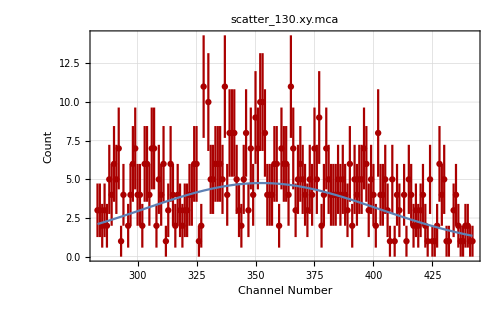
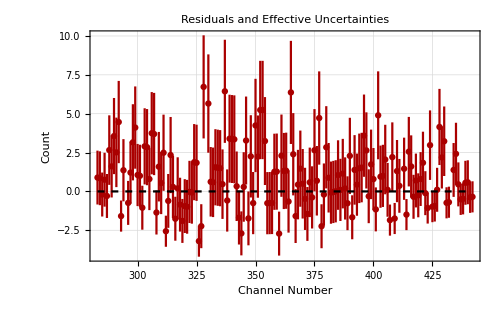
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
4.26556 | c= 
0.496153 | 
σ_y_max= 
4.28188 | σ_c= 
1.06997 | 
μ= 
352.543 | sigma= 
49.8594 | 
σ_μ= 
3.65033 | σ_sigma= 
40.9078 | χ^2/(n-4)= 
0.982867

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

```mathematica
AppendTo[xData,{130,mean,sigmean}];
```

```mathematica
Undo[]
```

scatter_130.xy.mca

n = 702

n = 51

Sorted data in order of increasing X values.

51 Y count values have had sigma values assigned.

Undo[] once to get rid of channel count sigmas.

Undo[] again to return to Scatter Data.

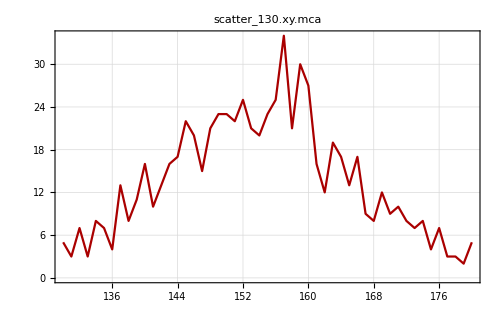

```mathematica
xy2y[]
```

```mathematica
GaussianCFit[]
```

n = 51

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
22.1546 | c= 
2.56721 | 
σ_y_max= 
2.06674 | σ_c= 
1.72782 | 
μ= 
153.98 | sigma= 
10.4402 | 
σ_μ= 
0.510594 | σ_sigma= 
1.39076 | Std. deviation= 
3.27685

Fit of (x,y±σ_y)

y_max= 
22.0973 | c= 
1.79622 | 
σ_y_max= 
1.56726 | σ_c= 
1.26034 | 
μ= 
153.896 | sigma= 
10.568 | 
σ_μ= 
0.532607 | σ_sigma= 
1.29822 | χ^2/(n-4)= 
0.736339

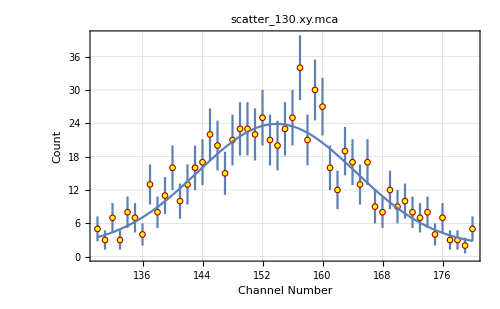
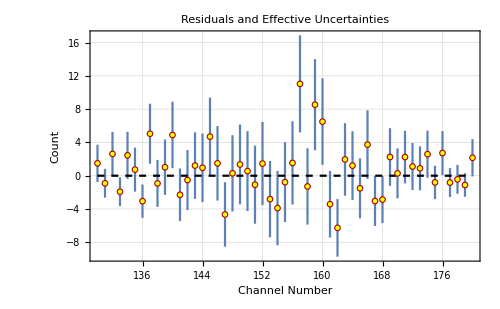
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
22.0973 | c= 
1.79622 | 
σ_y_max= 
1.56726 | σ_c= 
1.26034 | 
μ= 
153.896 | sigma= 
10.568 | 
σ_μ= 
0.532607 | σ_sigma= 
1.29822 | χ^2/(n-4)= 
0.736339

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

```mathematica
AppendTo[yData,{130,mean,sigmean}];
```

### 150 degrees

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 32a/32a/scatter_150.xy.mca

File comment header:

Spectrum #00005	3:20:09 PM 6/7/2018  Time: 854.28 ; XY Scatter Event Data
150 deg
X Ch	Y Ch

LoadFile::sorted: Data sorted in increasing x order.

Read 3311 data points.

n = 1704

Undo[] to return to previous data set.

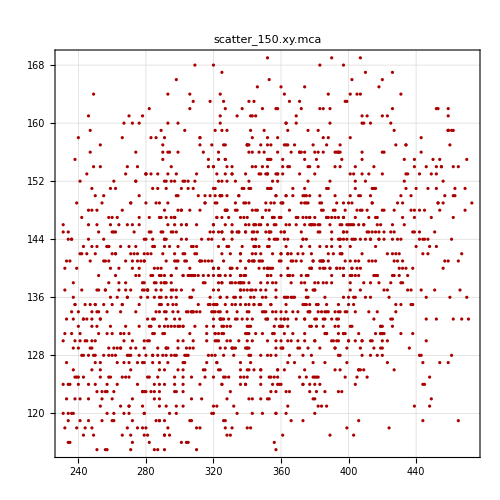

```mathematica
KeepXY[]
```

n = 237

Sorted data in order of increasing X values.

237 Y count values have had sigma values assigned.

Undo[] once to get rid of channel count sigmas.

Undo[] again to return to Scatter Data.

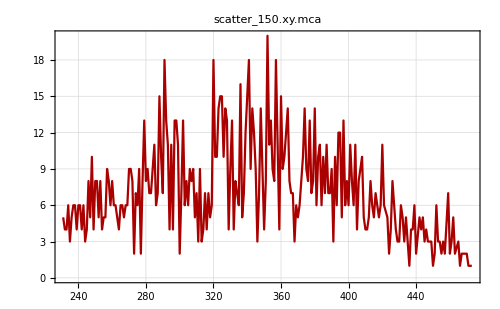

```mathematica
xy2x[]
```

```mathematica
NRangeRemove[#]&/@{75,77}
```

n= 229

1 point removed.

n= 228

1 point removed.

{Null,Null}

```mathematica
GaussianCFit[]
```

n = 228

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
15.0513 | c= 
-5.14919 | 
σ_y_max= 
22.4486 | σ_c= 
35.2525 | 
μ= 
334.964 | sigma= 
107.802 | 
σ_μ= 
3.11039 | σ_sigma= 
111.394 | Std. deviation= 
2.8249

Fit of (x,y±σ_y)

y_max= 
14.07 | c= 
-5.7903 | 
σ_y_max= 
85.9889 | σ_c= 
72.9871 | 
μ= 
330.726 | sigma= 
120.379 | 
σ_μ= 
3.60567 | σ_sigma= 
274.349 | χ^2/(n-4)= 
1.08132

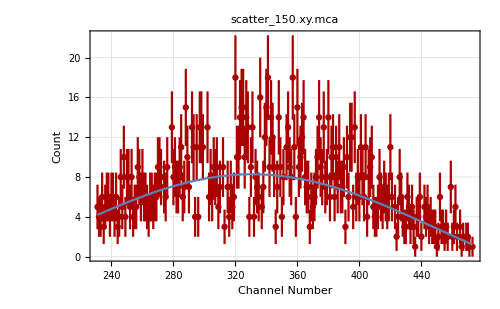
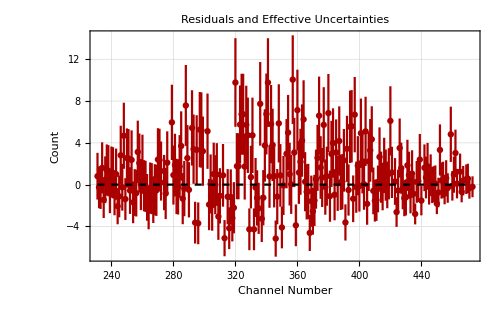
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
14.07 | c= 
-5.7903 | 
σ_y_max= 
85.9889 | σ_c= 
72.9871 | 
μ= 
330.726 | sigma= 
120.379 | 
σ_μ= 
3.60567 | σ_sigma= 
274.349 | χ^2/(n-4)= 
1.08132

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

```mathematica
AppendTo[xData,{150,mean,sigmean}];
```

```mathematica
Undo[]
```

scatter_150.xy.mca

n = 1704

n = 55

Sorted data in order of increasing X values.

55 Y count values have had sigma values assigned.

Undo[] once to get rid of channel count sigmas.

Undo[] again to return to Scatter Data.

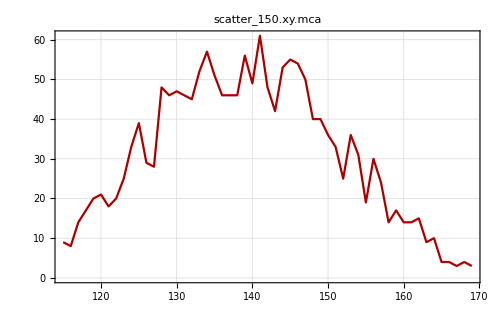

```mathematica
xy2y[]
```

```mathematica
GaussianCFit[]
```

n = 55

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
58.409 | c= 
-5.12061 | 
σ_y_max= 
5.37119 | σ_c= 
5.82291 | 
μ= 
138.821 | sigma= 
14.4829 | 
σ_μ= 
0.350487 | σ_sigma= 
1.38875 | Std. deviation= 
4.76571

Fit of (x,y±σ_y)

y_max= 
56.1225 | c= 
-3.08235 | 
σ_y_max= 
2.57393 | σ_c= 
2.9097 | 
μ= 
138.836 | sigma= 
13.7666 | 
σ_μ= 
0.357275 | σ_sigma= 
0.95142 | χ^2/(n-4)= 
0.716333

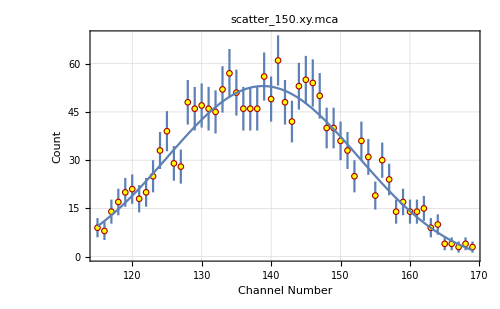
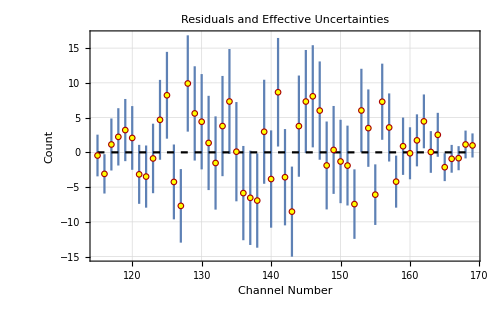
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
56.1225 | c= 
-3.08235 | 
σ_y_max= 
2.57393 | σ_c= 
2.9097 | 
μ= 
138.836 | sigma= 
13.7666 | 
σ_μ= 
0.357275 | σ_sigma= 
0.95142 | χ^2/(n-4)= 
0.716333

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

```mathematica
AppendTo[yData,{150,mean,sigmean}];
```

### Exporting NaI and Target Full-Energy Data

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["32a/na_full_energy.dat",yData];
```

```mathematica
Export["32a/target_full_energy.dat",xData];
```

We now recall the NaI and Target full-energy events into this notebook:

```mathematica
yData=Import["32a/na_full_energy.dat"];
```

```mathematica
xData=Import["32a/target_full_energy.dat"];
```

### Testing the Compton Energy equation

We tabulate the scattered photon energy for the full energy scattering events detected above using the scatter plots, propagating all errors including the Δθ = 1° and systematic uncertainties due to the calibration. For convenience, we obtain the total uncertainty by adding systematic and random errors in quadrature as defined in the calibration function above.

```mathematica
calEnergy=Table[calibration[{yData[[i]][[2]],yData[[i]][[3]]}],{i,1,Length[yData]}];
```

```mathematica
scatteredEnergy=Table[{π/180 yData[[i]][[1]],calEnergy[[i]][[1]],calEnergy[[i]][[2]],π/180 Sqrt[2]},{i,1,Length[yData]}]//N;
```

```mathematica
Export["32a/scattered_energy.dat",scatteredEnergy];
```

We tabulate the θ, E’ data:

```mathematica
scatteredTable=Join[{{"θ (rad)","E' (keV)"}},Table[{StringReplace["%1 ± %2",{"%1"->ToString[NumberForm[scatteredEnergy[[i]][[1]],3]],"%2"->ToString[NumberForm[scatteredEnergy[[i]][[4]],2]]}],StringReplace["%1 ± %2",{"%1"->ToString[NumberForm[scatteredEnergy[[i]][[2]],3]],"%2"->ToString[NumberForm[scatteredEnergy[[i]][[3]],2]]}]},{i,1,Length[scatteredEnergy]}]];
Grid[scatteredTable,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]
```

θ (rad) | E' (keV)
0.698 ± 0.025 | 514. ± 1.1
1.05 ± 0.025 | 399. ± 1.5
1.4 ± 0.025 | 325. ± 0.98
1.75 ± 0.025 | 270. ± 1.
2.09 ± 0.025 | 226. ± 0.85
2.27 ± 0.025 | 218. ± 0.88
2.62 ± 0.025 | 195. ± 0.66

We can now test the Compton energy relationship with scattering angle:

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 32a/32a/scattered_energy.dat

Read 7 data points.

```mathematica
(* Transforming data to linear form *)
```

```mathematica
xnew[ x_, y_ ] := Sin[1/2 x]^2
ynew[ x_, y_ ] := 1/y

DataTransform[]
```

All 7 points transformed.

```mathematica
LinearFit[]
```

n = 7

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
0.00150585 | b= 
0.00382984 | 
σ_a= 
0.0000428827 | σ_b= 
0.0000690708 | Std. deviation= 
0.0000515984

Fit of (x,y±σ_y)

a= 
0.00150214 | b= 
0.00383534 | 
σ_a= 
4.94005×10^-6 | σ_b= 
0.0000137886 | χ^2/(n-2)= 
13.9103

Fit of (x±σ_x,y±σ_y)

a= 
0.00149672 | b= 
0.00385771 | 
σ_a= 
0.0000289197 | σ_b= 
0.0000458586 | χ^2/(n-2)= 
1.6505

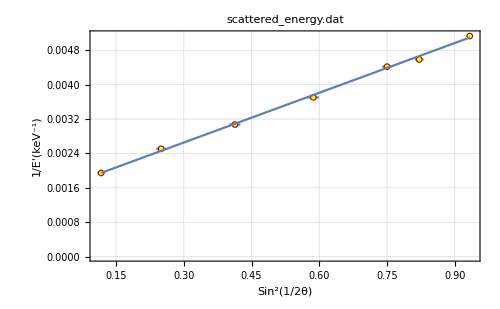
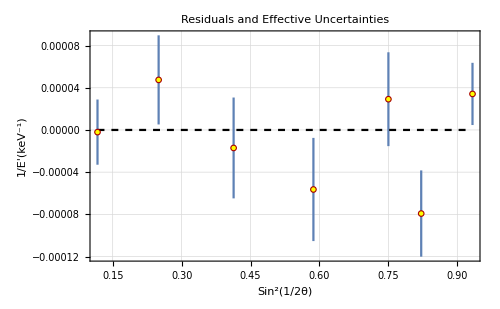
-Graphics-
-Graphics-
y(x) = a + b x
a= 
0.00149672 | b= 
0.00385771 | 
σ_a= 
0.0000289197 | σ_b= 
0.0000458586 | χ^2/(n-2)= 
1.6505

```mathematica
LinearDifferencePlot[FrameLabel->{"Sin^2(1/2θ)","1/E'(keV^-1)"}]
```

We obtain a good linear fit, indicating that the Compton relationship indeed holds. Furthermore,

```mathematica
k0=1/a{1,siga/a} (* keV *)
```

{668.126,12.9096}

```mathematica
me=2/b {1,sigb/b}(* keV *)
```

{518.442,6.16299}

We therefore have estimates for k_0=668 ± 13keV and m_e=518.4 ± 6.2 keV, which are within error of the expected values for the full-energy photons for Cs-137 and the rest mass of the electron, respectively. This again indicates consistency with the Compton energy relationship with scattering angle.

## Target scintillator calibration

Unfortunately, only the Cs-137 spectrum has a discernible, single Compton edge. The Na-22 and Ba-133 calibration data have noise issues making it impossible to accurately identify the Compton edge, and the Co-60 spectrum has two full-energy events, making it difficult to distinguish the superposed Compton edges.

We use the ComptonSpectra1.nb notebook from Experiment 30b and fit the Cs-137 Compton edge:

```mathematica
ComptonFit[0.661,5000,450]
```

n = 319

y(x) = Compton spectrum from a photon with energy k_0, scaled in X and Y and convolved with the scintillator resolution e_pe(energy/photoelectron).

Fit of (x,y)  (unweighted)

K0 (MeV) = 
0.661 | Tedge (MeV) = 
0.476728 | 
EPE (eV/photoelectron) = 
9866.84 | sigEPE = 
30.7165 | 
Xscale (channels/MeV) = 
954.749 | sigXscale = 
0.184448 | 
Yscale = 
(counts/channel)/(probability/MeV)
102.213 | sigYscale = 
0.0885552 | 
Yoffset (counts/channel) = 
3.3048 | sigYoffset = 
0.136455 | 
Xedge (channel) = 
455.156 | sigXedge = 
0.0879317 | Std. deviation = 
145.722

Fit of (x,y±σ_y)

K0 (MeV) = 
0.661 | Tedge (MeV) = 
0.476728 | 
EPE (eV/photoelectron) = 
9706.54 | sigEPE = 
360.523 | 
Xscale (channels/MeV) = 
953.657 | sigXscale = 
1.8013 | 
Yscale = 
(counts/channel)/(probability/MeV)
102.133 | sigYscale = 
0.618746 | 
Yoffset (counts/channel) = 
2.5015 | sigYoffset = 
0.221614 | 
Xedge (channel) = 
454.635 | sigXedge = 
0.858732 | χ^2 = 
0.970868

Fit of (x±σ_x,y±σ_y)

K0 (MeV) = 
0.661 | Tedge (MeV) = 
0.476728 | 
EPE (eV/photoelectron) = 
9706.37 | sigEPE = 
360.519 | 
Xscale (channels/MeV) = 
953.657 | sigXscale = 
1.8013 | 
Yscale = 
(counts/channel)/(probability/MeV)
102.133 | sigYscale = 
0.618745 | 
Yoffset (counts/channel) = 
2.50152 | sigYoffset = 
0.221614 | 
Xedge (channel) = 
454.635 | sigXedge = 
0.858731 | χ^2 = 
0.970863

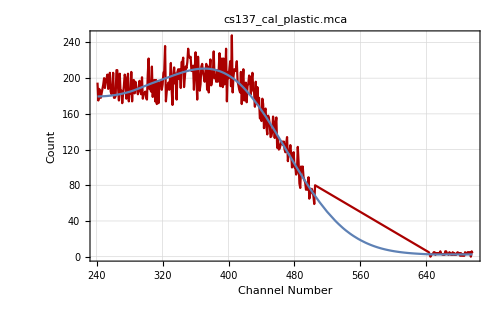
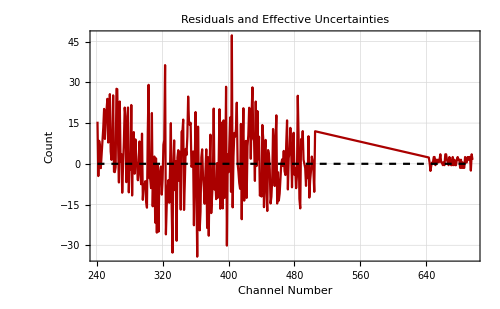
-Graphics-
-Graphics-
y(x) = Compton spectrum from a photon with energy k_0, scaled in X and Y and convolved with the scintillator resolution e_pe(energy/photoelectron).

K0 (MeV) = 
0.661 | Tedge (MeV) = 
0.476728 | 
EPE (eV/photoelectron) = 
9706.37 | sigEPE = 
360.519 | 
Xscale (channels/MeV) = 
953.657 | sigXscale = 
1.8013 | 
Yscale = 
(counts/channel)/(probability/MeV)
102.133 | sigYscale = 
0.618745 | 
Yoffset (counts/channel) = 
2.50152 | sigYoffset = 
0.221614 | 
Xedge (channel) = 
454.635 | sigXedge = 
0.858731 | χ^2 = 
0.970863

```mathematica
LinearDifferencePlot[FrameLabel->{"Channel Number","Count"}]
```

We obtain a reasonably good fit, and a rough estimate of the calibration given by Xscale above.

```mathematica
calibrationTarget[channel_]:=channel[[1]]/953.6573547506756*1000{1,Sqrt[(1.8013021195385253/953.6573547506756)^2+(channel[[2]]/channel[[1]])^2]};
```

```mathematica
calEnergyTarget=Table[calibrationTarget[{xData[[i]][[2]],xData[[i]][[3]]}],{i,1,Length[xData]}];
```

```mathematica
targetEnergy=Table[{π/180 xData[[i]][[1]],calEnergyTarget[[i]][[1]],calEnergyTarget[[i]][[2]],π/180 Sqrt[2]},{i,1,Length[xData]}]//N;
```

```mathematica
Export["32a/target_energy.dat",scatteredEnergy];
```

We tabulate the θ, E data:

```mathematica
targetTable=Join[{{"θ (rad)","E (keV)"}},Table[{StringReplace["%1 ± %2",{"%1"->ToString[NumberForm[targetEnergy[[i]][[1]],3]],"%2"->ToString[NumberForm[targetEnergy[[i]][[4]],2]]}],StringReplace["%1 ± %2",{"%1"->ToString[NumberForm[targetEnergy[[i]][[2]],3]],"%2"->ToString[NumberForm[targetEnergy[[i]][[3]],2]]}]},{i,1,Length[targetEnergy]}]];
Grid[targetTable,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]
```

θ (rad) | E (keV)
0.698 ± 0.025 | 139. ± 1.2
1.05 ± 0.025 | 243. ± 1.8
1.4 ± 0.025 | 317. ± 1.5
1.75 ± 0.025 | 366. ± 4.7
2.09 ± 0.025 | 378. ± 4.5
2.27 ± 0.025 | 370. ± 3.9
2.62 ± 0.025 | 347. ± 3.8

### Consistency with conservation of energy

We add the scattered photon energy and the outgoing electron energy for each angle, and expect to obtain data points consistent with a constant at 661 keV if the interactions are consistent with energy conservation.

```mathematica
totalEnergy=Table[{scatteredEnergy[[i]][[1]],scatteredEnergy[[i]][[2]]+targetEnergy[[i]][[2]],Sqrt[(scatteredEnergy[[i]][[3]])^2+(targetEnergy[[i]][[3]])^2],scatteredEnergy[[i]][[4]]},{i,1,Length[scatteredEnergy]}];
```

```mathematica
Export["32a/conservation.dat",totalEnergy];
```

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 32a/32a/conservation.dat

Read 7 data points.

```mathematica
LinearFit[]
```

n = 7

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
704.445 | b= 
-52.5747 | 
σ_a= 
19.8212 | σ_b= 
10.9425 | Std. deviation= 
18.4575

Fit of (x,y±σ_y)

a= 
691.676 | b= 
-45.0944 | 
σ_a= 
2.31791 | σ_b= 
1.66556 | χ^2/(n-2)= 
34.0009

Fit of (x±σ_x,y±σ_y)

a= 
696.317 | b= 
-48.6362 | 
σ_a= 
2.90004 | σ_b= 
1.99282 | χ^2/(n-2)= 
27.7605

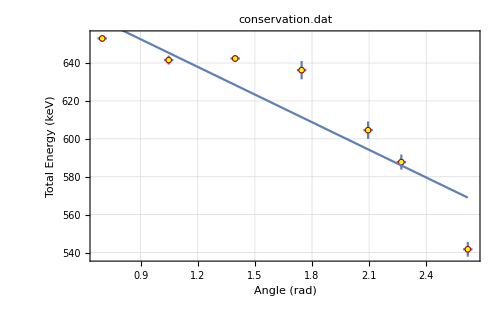
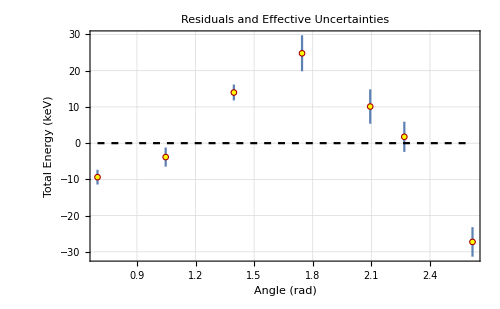
-Graphics-
-Graphics-
y(x) = a + b x
a= 
696.317 | b= 
-48.6362 | 
σ_a= 
2.90004 | σ_b= 
1.99282 | χ^2/(n-2)= 
27.7605

```mathematica
LinearDifferencePlot[FrameLabel->{"Angle (rad)","Total Energy (keV)"}]
```

This is clearly not consistent with a constant, indicating that the larger angle data points either contain significant systematic errors, or some of the larger angle data points are skewed by the presence of Compton scatters in the NaI scintillator. This would make sense, seeing as we found it much more difficult to extract the full-energy events from the scatter plots for the large-angle measurements. We remove the large-angle measurements and attempt the same fit.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{0.632423,1.87}

n= 4

3 points removed.

```mathematica
LinearFit[]
```

n = 4

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
660.566 | b= 
-14.1432 | 
σ_a= 
5.86885 | σ_b= 
4.57592 | Std. deviation= 
3.57214

Fit of (x,y±σ_y)

a= 
662.484 | b= 
-15.3625 | 
σ_a= 
3.44424 | σ_b= 
3.11769 | χ^2/(n-2)= 
2.69796

Fit of (x±σ_x,y±σ_y)

a= 
662.547 | b= 
-15.4419 | 
σ_a= 
3.54747 | σ_b= 
3.20908 | χ^2/(n-2)= 
2.61749

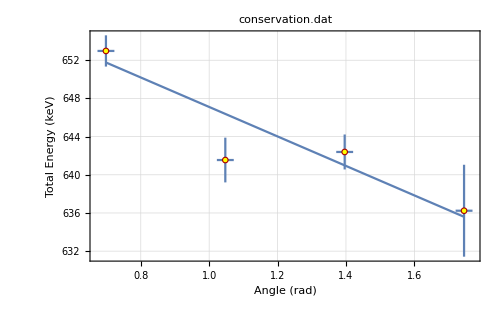
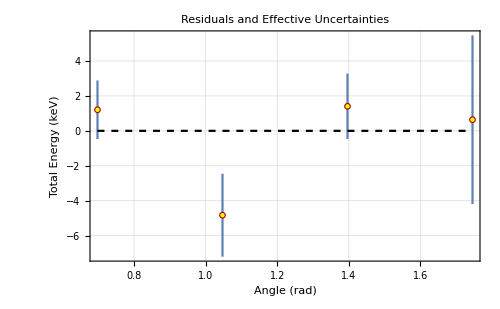
-Graphics-
-Graphics-
y(x) = a + b x
a= 
662.547 | b= 
-15.4419 | 
σ_a= 
3.54747 | σ_b= 
3.20908 | χ^2/(n-2)= 
2.61749

```mathematica
LinearDifferencePlot[FrameLabel->{"Angle (rad)","Total Energy (keV)"}]
```

This is still not consistent with a slope of 0 (constant) but we have a much better fit with a much smaller slope, with the intercept within error of the Cs-137 full-energy events. This indeed indicates as suspected earlier, the presence of systematic errors in the larger-angle measurements due to Compton scattering in the NaI scintillator difficult to extract from the full-energy events when converting the scatter plot to energy peak data.

## Appendix - Calibration spectra and scatter plot

### Typical NaI scintillator calibration spectrum - Cs-137

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 32a/32a/cs137_cal_na.mca

File comment header:

Spectrum #00013	1:30:11 PM 6/7/2018  Time: 445.08 ; MCA 2

Ch  	Count

Read 1024 data points.

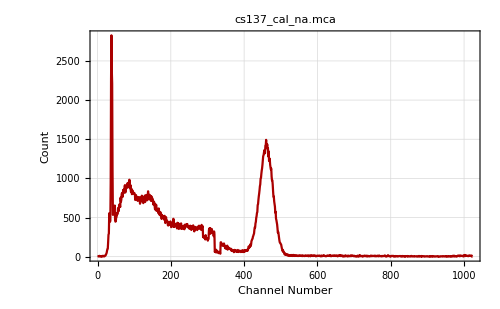

```mathematica
LinearDataPlot[FrameLabel->{"Channel Number","Count"}]
```

### Typical NaI scintillator Compton scattering spectrum (80°) - Cs-137

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 32a/32a/scatter_80.y.mca

File comment header:

Spectrum #00008	4:06:47 PM 6/7/2018  Time: 1454.27 ; NaI (outgoing photon) Detector
80 deg
Ch  	Count

Read 1024 data points.

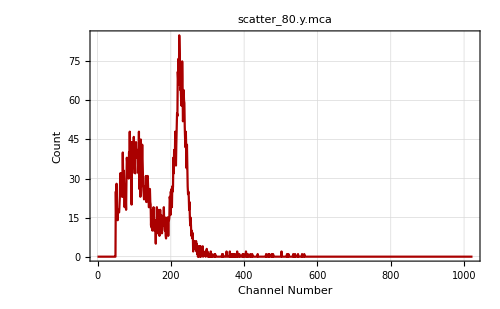

```mathematica
LinearDataPlot[FrameLabel->{"Channel Number","Count"}]
```

### Typical Plastic scintillator calibration spectrum - Cs-137

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 32a/32a/cs137_cal_plastic.mca

File comment header:

Spectrum #00015	1:48:54 PM 6/7/2018  Time: 968.44 ; MCA 1

Ch  	Count

Read 1024 data points.

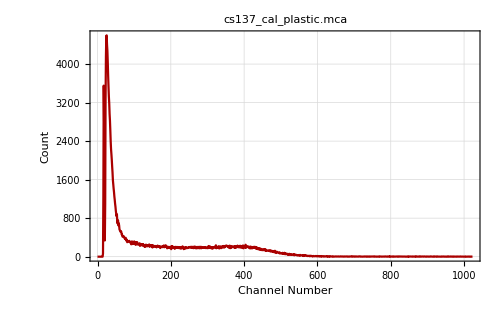

```mathematica
LinearDataPlot[FrameLabel->{"Channel Number","Count"}]
```

### Typical Plastic scintillator Compton scattering spectrum (80°) - Cs-137

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 32a/32a/scatter_80.x.mca

File comment header:

Spectrum #00008	4:06:47 PM 6/7/2018  Time: 1454.27 ; Plastic (target) Detector
80 deg
Ch  	Count

Read 1024 data points.

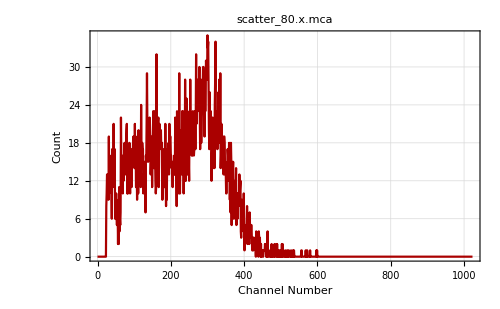

```mathematica
LinearDataPlot[FrameLabel->{"Channel Number","Count"}]
```

### Typical Compton scatter plots - Cs-137

#### 40°

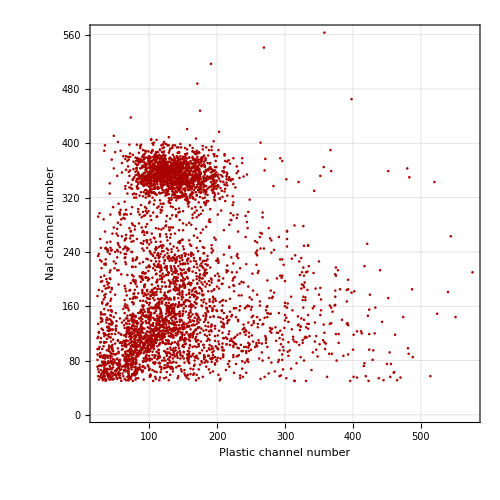

### 80°

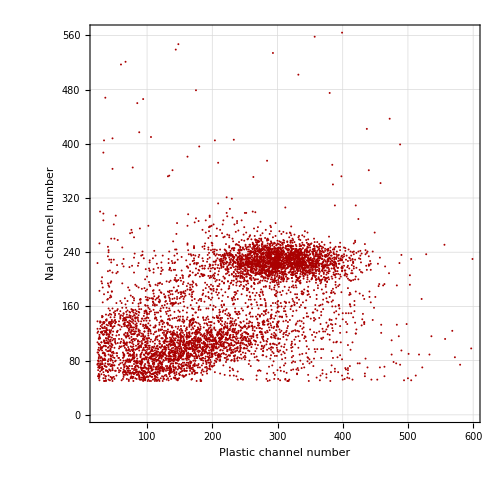

### 150°